```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/blogit"]
```

/Users/peeter/project/figures/blogit

```mathematica
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16];
```

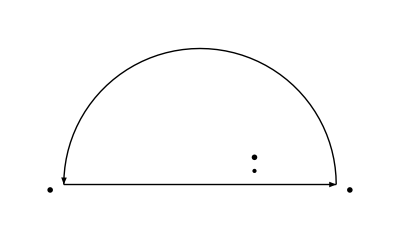

-Graphics-

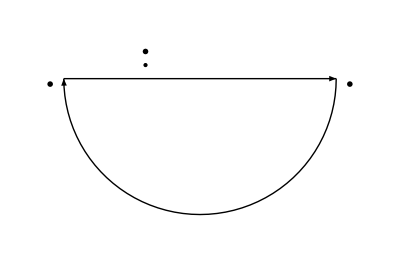

```mathematica
ClearAll[R, lineArrow, xrange1, r, semicircleArrow, greensHelmholtzFig1, greensHelmholtzFig1a, greensHelmholtzFig1b, epsilon, k]
R=5; 
k = 2;
epsilon = 0.5;
xrange1 = {{-R,0},{R, 0}};

lineArrow[sk_, se_, t_]:=Graphics[{
Thick,Arrow[xrange1],
Text[MaTeX["-R"], {-1.1 R, -0.2}],
Text[MaTeX["R"], {1.1 R, -0.2}],
Text[MaTeX[t], {sk k, 2 se epsilon}],
PointSize -> Large,

Point[{sk k,se epsilon}]
}];

semicircleArrow[a_, s_, u_]:=Graphics[{Thick,Arrow[Table[{a Cos[t],a Sin[t]},{t,s,u,(u-s)/50}]]}]

greensHelmholtzFig1 = Show[lineArrow[1, 1,"k + j \\epsilon"],semicircleArrow[R, 0,Pi],AspectRatio->Automatic,PlotRange->{{-R-1,R+1},{-1,R+1}},Axes->False,Ticks->None,Frame->False]

greensHelmholtzFig1a = Show[lineArrow[1, 1,"k + j \\epsilon, \\epsilon > 0"],semicircleArrow[R, 0, Pi],AspectRatio->Automatic,PlotRange->{{-R-1,R+1},{-1,R+1}},Axes->False,Ticks->None,Frame->False]

greensHelmholtzFig1b = Show[lineArrow[-1, 1, "-k - j \\epsilon, \\epsilon < 0"],semicircleArrow[R, 0,-Pi],AspectRatio->Automatic,PlotRange->{{-R-1,R+1},{-R-1,2}},Axes->False,Ticks->None,Frame->False]
```

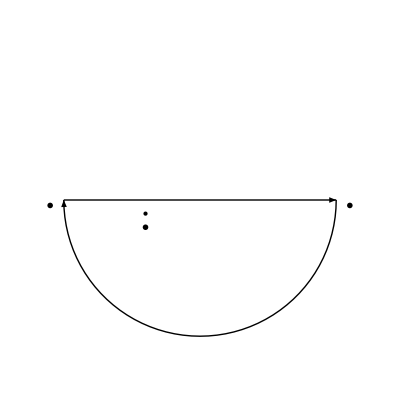

```mathematica
ClearAll[greensHelmholtzFig2]

(*greensHelmholtzFig2 = Show[lineArrow[-1, -1, "-k - j \\epsilon"],semicircleArrow[R, 0, -Pi],AspectRatio->Automatic,PlotRange->{{-R-1,R+1},{-R-1,R+1}},Axes->False,Ticks->None,Frame->False]*)
greensHelmholtzFig2 = Show[lineArrow[-1, -1, "-k - j \\epsilon, \\epsilon > 0"],semicircleArrow[R, 0, -Pi],AspectRatio->Automatic,PlotRange->{{-R-1,R+1},{-R-1,R+1}},Axes->False,Ticks->None,Frame->False]
```

```mathematica
peeters`exportForLatex["greensHelmholtzFig1",greensHelmholtzFig1]
peeters`exportForLatex["greensHelmholtzFig2",greensHelmholtzFig2]
peeters`exportForLatex["greensHelmholtzFig1a",greensHelmholtzFig1a]
peeters`exportForLatex["greensHelmholtzFig1b",greensHelmholtzFig1b]
```

{greensHelmholtzFig1.eps,greensHelmholtzFig1pn.png}

{greensHelmholtzFig2.eps,greensHelmholtzFig2pn.png}

{greensHelmholtzFig1a.eps,greensHelmholtzFig1apn.png}

{greensHelmholtzFig1b.eps,greensHelmholtzFig1bpn.png}